```mathematica
(*Transforma tensor vetorial de voigth em tensor  3x3*)
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
(*Transforma tensor  3x3 em tensor vetorial de voigth *)
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[2,3]],2sig[[1,3]],2sig[[1,2]]}
ComputeS[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
ComputeJ2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
ComputeI1[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
N[Tr[cart]]
]
P={{2/3,-1/3,-1/3,0,0,0},{-1/3,2/3,-1/3,0,0,0},{-1/3,-1/3,2/3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,2,0},{0,0,0,0,0,2}}//N;
ax[sigma_]:=A/3 {1,1,1,0,0,0}+1/(2Sqrt[ComputeJ2[sigma]])ComputeS[sigma]//.subst2
dadsigmax[sigma_]:=P 1/(2 Sqrt[ComputeJ2[sigma]])-1/(4 ComputeJ2[sigma]^(3/2))Outer[Times,ComputeS[sigma],ComputeS[sigma]]
(*Calcula autovalores e autovetores e ordena na ordem decrescente*)
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];

F1HWCylDruckerPrager[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy,A,B,c},
xiint=xi;
rhoint=Sqrt[2] (B c-A xi);
rhoint=√2 B c-√(2/3) A xi;
betaint=beta;
N[{xiint,rhoint,betaint}]
]
FDP[I1_,J2_]:=(Sqrt[J2]+A I1/3 -c B)
ApplyStrainComputeSigmaDep[epst_,epsp_,subst2_]:=Block[{invCe,R,Q,invQ,sig1,sig2,sig3,epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,I1,J2,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},

Ce=N[{{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}}]//.subst2;
invCe=N[{{(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),0,0,0},{0,0,0,1/G,0,0},{0,0,0,0,1/G,0},{0,0,0,0,0,1/G}}]//.subst2;

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

epsetrial=(epstint-epspint);

sigma=Ce.epsetrial;

I1=ComputeI1[sigma];
J2=ComputeJ2[sigma];
yield=FDP[I1,J2]//.subst2;

If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,

xitrial=I1/Sqrt[3];
rhotrial=Sqrt[2J2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=ArcTan[(√3 (-sig2+sig3))/(-2 sig1+sig2+sig3)]//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
xisol=1/(6 (G+A^2 K))(-3 A K (2 sig1-sig2-sig3) Cos[betasol]+√3 (6 A B c K+2 G (sig1+sig2+sig3)-3 A K (sig2-sig3) Sin[betasol]))//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
proj=HW[F1HWCylDruckerPrager[{xisol,rho,betasol}]]//.subst2;
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
asol=ax[sigprojvoigth]//.subst2;
dadsigg=dadsigmax[sigprojvoigth]//.subst2;
epse=invCe.sigprojvoigth;
gamma=Norm[epsetrial-epse]/Norm[asol];

dadsigg=dadsigmax[sigma]//.subst2;
CT=Ce.((IdentityMatrix[6]-(Outer[Times,asol,asol].Ce)/(asol.Ce.asol)));
T=(IdentityMatrix[6]- gamma dadsigg.Ce );
Dep=CT.T;

acone=Sqrt[J2]-gamma G//.subst2;

If[acone<0,

(*Print["acone = ",acone];*)
II={1,1,1,0,0,0};
 eq=(c B/A - I1/3 +K dgamma A) //.subst2;
solgamma=NSolve[eq==0,dgamma][[1,1,2]];
Dep=0Outer[Times,II,II];
full=FromVoigtToCart[sigma];

If[J2≤0,
(*no caso de tracao hidrostatica j2 = 0 *)
sn1=0;
,
sn1=(1-G solgamma/Sqrt[J2])(full-1/3 Tr[full]IdentityMatrix[3])//.subst2;
];

pn1=I1/3-K A solgamma//.subst2;
updatedstress=sn1+pn1 IdentityMatrix[3];
sigprojvoigth=FromCartToVoigt[updatedstress];
epse=invCe.sigprojvoigth;
gamma=solgamma;
];
];
Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
{sx,sy,tauxy}=sigproj2D;
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D,gamma}//.subst2

];
(*Compute2DShape*)
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[serendipity==True,
psis={
(1-xi)(1-eta)(-xi-eta-1)/4,(*1*)(1+xi)(1-eta)(xi-eta-1)/4,(*2*)(1+xi)(1+eta)(xi+eta-1)/4,(*3*)(1-xi)(1+eta)(-xi+eta-1)/4,(*4*)
(1-xi^2)(1-eta)/2,(*5*)(1+xi)(1-eta^2)/2,(*6*)(1-xi^2)(1+eta)/2,(*7*)(1-xi)(1-eta^2)/2(*8*)
};
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
(****************************************************************************************)
(*IntegrationRule*)
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
{pts,w}=Transpose[GaussianQuadratureWeights[porder+2,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
N[matpsts]
];
(****************************************************************************************)
(*CalcStiff*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob,Fe2,Fglob2},
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Fglob2=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe,Fe2}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
Fglob2[[2rowglob+fu]]+=Fe2[[2 i+fu]];
Fglob2[[2rowglob]]+=Fe2[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob,Fglob2}
];
(*Compute one dimension shape functions*)
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
(*Find node id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]]-1,j]]=0;
Ek[[j,2ids[[i]]-1]]=0;
];
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=1;
Ef[[2ids[[i]]-1]]=val;
,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]],j]]=0;
Ek[[j,2ids[[i]]]]=0;
];
Ek[[2ids[[i]],2ids[[i]]]]=1;
Ef[[2ids[[i]]]]= val;
];
];
{Ek,Ef}
];
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,BB,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint,ef2},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
BB={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];
(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)
{stress,Dep,epse,gamma}=ApplyStrainComputeSigmaDep[epst,epsp,subst2];
epspeint=epst-epse;
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
AppendTo[epsppost,{x,y,epspeint}];
AppendTo[stressppost,{x,y,stress}];
AppendTo[dgamma,{x,y,gamma}];
(*Element Stiffness Matrix contribution*)
ek=(Transpose[BB].Dep.BB)weight DetJ;
(*Element Internal force vector contribution*)
ef=(Transpose[BB].stress)weight DetJ;
ef2=(Transpose[NShapes].{0,-bodyforce})weight DetJ;
{ek,ef,ef2}
];

(*CalcStiff - Assemble the element stiffness matrix and internal force vectors*)
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{ef2,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
ef2=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef,ef2}+=Contribute[data];
,{i,1,npts}
];
{ek,ef,ef2}
];

ComputeSolNoInterpolation[topol_,coords_,order_,coefs_,eltype_,scale_]:=Block[{elvecnorm,diplacenormvec,cx,cy,ux,uy,,displacevec,elvec,X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
displacevec={};
diplacenormvec={};
Table[
elvec={};
(*elvecnorm={};*)
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
cx=coords[[id,1]] ;
cy=coords[[id,2]] ;
ux=scale coefs[[2 id-1]] ;
 uy=scale coefs[[2id]] ;
AppendTo[elvec,{{cx,cy},{ux+cx,uy+cy}}];
AppendTo[diplacenormvec,{cx,cy,Norm[{ux/scale,uy/scale}]}];
,{j,1,kk}];
AppendTo[displacevec,elvec];
(*AppendTo[diplacenormvec,elvec];*)
,{i,1,nels}];
{displacevec,diplacenormvec}
]
```

{{375.,500.},{250.,500.},{250.,475.},{375.,462.5},{312.5,500.},{250.,487.5},{312.5,470.438},{375.,481.25}}

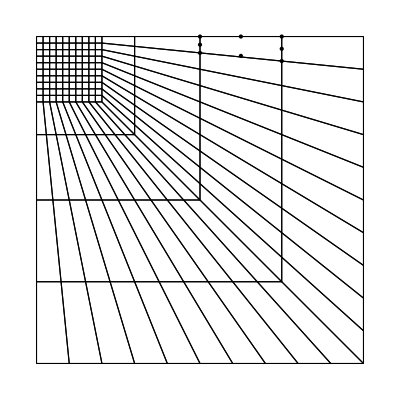

2

{1,3,5,6,10,13,16,20,25,33,39,46,53,62,69,84,94,109,124,140,155}

{155,160,173,189,211,240,313,364,430,444,454,471,480,496,504,519,526,538,544,554,559,566,570,576,579,583,585,587,589}

{543,553,558,567,571,577,580,584,586,588,589}

{1,2,4,7,9,14,15,19,24,32,38,45,54,61,70,85,95,110,123,139,154}

```mathematica
pack=Developer`ToPackedArray;

topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/setx566dvgx3urx/mesh-els-strip-foot-structured4.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/mxelbdwug4yv3lr/mesh-nodes-strip-foot-structured4.txt?dl=1","Table"];
(*topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/gz1rastmoemiaz0/mesh-els-strip-foot-structured-ninenode.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/vaz8ljhr79hxpnt/mesh-nodes-strip-foot-structured-ninenode.txt?dl=1","Table"];*)

nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nnodes]}}];
Show[meshVis1];
el=60;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]
order=2
serendipity=False;

a=500;
b2=50;
x0=0.;xf=a;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=a;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=0;xf=b2;
y0=a;yf=a;
searchpathupline=Table[{x,y0},{x,x0,xf,(xf-x0)/ndivs}];
x0=a;xf=a;
y0=0;yf=a;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idssup=FindIds[nnodes,searchpathupline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


subst2={c->490.,phi->20/180. Pi,young->10^7. (*kPa*),nu->0.48 ,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),A->3 Tan[phi]/Sqrt[9+12 Tan[phi]^2],
B->3 /Sqrt[9+12 Tan[phi]^2]};


f[x_]:=15 c//.subst2 ;
FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};

lamb=1;
diff=10;
l=0.5;
counterout=1;
tol1=10^-2;
tol2=10^-6;
While[Abs[diff]>tol1 && counterout≤30,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol2,

epsppost={};
dgamma={};
stressppost={};
globalcounter=1;
{KT,FINT,FEXTB}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
FEXT+=FEXTB;
imposex=1;
imposey=2;

R=lamb  FEXT-FINT;

{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];
a=dwb.dwb;
b=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
dlamb=Solve[a x^2 +b x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];

Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[lamb FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb];
counter++;
];
diff=Abs[lamb-lambn];
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];
id=FindIds[nnodes,{{0,500}}][[1]];
AppendTo[sol2,{-displace[[id 2]]/100, f[x] lamb/c//.subst2}];

AppendTo[sol3,epspvec];
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

i = 1 | lamb = 1 | lambn = 1 | diff = 10

Iteration number = 1  |R|/|FE| =  2.00155  |Δu|/|u| = 1.  |R| =  121269. |dw| = 0.5 | dlamb = -0.500387 | lamb = 0.499613

Iteration number = 2  |R|/|FE| =  0.211597  |Δu|/|u| = 0.0426078  |R| =  12622.4 |dw| = 0.0213039 | dlamb = -0.007704 | lamb = 0.491909

Iteration number = 3  |R|/|FE| =  0.218732  |Δu|/|u| = 0.0131141  |R| =  12979. |dw| = 0.00655707 | dlamb = -0.00260186 | lamb = 0.489307

Iteration number = 4  |R|/|FE| =  0.0722077  |Δu|/|u| = 0.00327363  |R| =  4280.57 |dw| = 0.00163682 | dlamb = -0.000464277 | lamb = 0.488842

Iteration number = 5  |R|/|FE| =  0.0102062  |Δu|/|u| = 0.000236753  |R| =  605.015 |dw| = 0.000118377 | dlamb = -0.0000176424 | lamb = 0.488825

Iteration number = 6  |R|/|FE| =  0.000856978  |Δu|/|u| = 8.6325×10^-6  |R| =  50.8009 |dw| = 4.31625×10^-6 | dlamb = -6.75511×10^-7 | lamb = 0.488824

Iteration number = 7  |R|/|FE| =  9.27817×10^-8  |Δu|/|u| = 1.70829×10^-9  |R| =  0.00550002 |dw| = 8.54144×10^-10 | dlamb = -1.44479×10^-10 | lamb = 0.488824

i = 2 | lamb = 0.488824 | lambn = 1 | diff = 0.511176

Iteration number = 1  |R|/|FE| =  0.0101265  |Δu|/|u| = 0.504616  |R| =  1100.96 |dw| = 0.5 | dlamb = 0.407708 | lamb = 0.896533

Iteration number = 2  |R|/|FE| =  0.762676  |Δu|/|u| = 0.106446  |R| =  74531.7 |dw| = 0.103527 | dlamb = -0.0906873 | lamb = 0.805845

Iteration number = 3  |R|/|FE| =  0.420321  |Δu|/|u| = 0.0241075  |R| =  40372.5 |dw| = 0.0233349 | dlamb = -0.0137903 | lamb = 0.792055

Iteration number = 4  |R|/|FE| =  0.134559  |Δu|/|u| = 0.00533524  |R| =  12895.8 |dw| = 0.00516011 | dlamb = -0.00176602 | lamb = 0.790289

Iteration number = 5  |R|/|FE| =  0.0490269  |Δu|/|u| = 0.00137767  |R| =  4696.49 |dw| = 0.0013322 | dlamb = -0.000357156 | lamb = 0.789932

Iteration number = 6  |R|/|FE| =  0.0121014  |Δu|/|u| = 0.000696278  |R| =  1159.02 |dw| = 0.000673246 | dlamb = -0.000145804 | lamb = 0.789786

Iteration number = 7  |R|/|FE| =  0.00214732  |Δu|/|u| = 0.000175612  |R| =  205.654 |dw| = 0.0001698 | dlamb = -0.0000332875 | lamb = 0.789753

Iteration number = 8  |R|/|FE| =  0.00016183  |Δu|/|u| = 0.0000345887  |R| =  15.4988 |dw| = 0.0000334439 | dlamb = -6.0931×10^-6 | lamb = 0.789747

Iteration number = 9  |R|/|FE| =  0.0000250244  |Δu|/|u| = 5.34041×10^-6  |R| =  2.39663 |dw| = 5.16365×10^-6 | dlamb = -8.55398×10^-7 | lamb = 0.789746

Iteration number = 10  |R|/|FE| =  3.68222×10^-6  |Δu|/|u| = 7.13029×10^-7  |R| =  0.352652 |dw| = 6.89429×10^-7 | dlamb = -1.04093×10^-7 | lamb = 0.789746

i = 3 | lamb = 0.789746 | lambn = 0.488824 | diff = 0.300922

Iteration number = 1  |R|/|FE| =  0.0407302  |Δu|/|u| = 0.343776  |R| =  5244.88 |dw| = 0.5 | dlamb = 0.272122 | lamb = 1.06187

Iteration number = 2  |R|/|FE| =  0.562275  |Δu|/|u| = 0.0841362  |R| =  66274.2 |dw| = 0.119848 | dlamb = -0.0899119 | lamb = 0.971956

Iteration number = 3  |R|/|FE| =  0.270907  |Δu|/|u| = 0.0196009  |R| =  31482.6 |dw| = 0.0277587 | dlamb = -0.0136552 | lamb = 0.9583

Iteration number = 4  |R|/|FE| =  0.168921  |Δu|/|u| = 0.00545275  |R| =  19590.1 |dw| = 0.0077155 | dlamb = -0.00197693 | lamb = 0.956323

Iteration number = 5  |R|/|FE| =  0.0436572  |Δu|/|u| = 0.00272751  |R| =  5058.98 |dw| = 0.00385771 | dlamb = -0.000763735 | lamb = 0.95556

Iteration number = 6  |R|/|FE| =  0.0109093  |Δu|/|u| = 0.00383973  |R| =  1263.14 |dw| = 0.00542883 | dlamb = -0.00076974 | lamb = 0.95479

Iteration number = 7  |R|/|FE| =  0.013157  |Δu|/|u| = 0.00380671  |R| =  1522.14 |dw| = 0.00538005 | dlamb = -0.000787902 | lamb = 0.954002

Iteration number = 8  |R|/|FE| =  0.00794473  |Δu|/|u| = 0.00285307  |R| =  918.565 |dw| = 0.00403103 | dlamb = -0.000587204 | lamb = 0.953415

Iteration number = 9  |R|/|FE| =  0.00837019  |Δu|/|u| = 0.000321337  |R| =  967.763 |dw| = 0.000454005 | dlamb = 6.44169×10^-6 | lamb = 0.953421

Iteration number = 10  |R|/|FE| =  0.00207024  |Δu|/|u| = 0.000562432  |R| =  239.397 |dw| = 0.000794693 | dlamb = 0.000138012 | lamb = 0.953559

Iteration number = 11  |R|/|FE| =  0.000171482  |Δu|/|u| = 0.0000133883  |R| =  19.8296 |dw| = 0.000018917 | dlamb = -3.47628×10^-6 | lamb = 0.953556

Iteration number = 12  |R|/|FE| =  0.0000887415  |Δu|/|u| = 0.0000448043  |R| =  10.2617 |dw| = 0.0000633061 | dlamb = -0.0000101202 | lamb = 0.953546

Iteration number = 13  |R|/|FE| =  0.0000170941  |Δu|/|u| = 6.19322×10^-6  |R| =  1.97668 |dw| = 8.7507×10^-6 | dlamb = -9.03334×10^-7 | lamb = 0.953545

Iteration number = 14  |R|/|FE| =  9.01191×10^-6  |Δu|/|u| = 2.78223×10^-6  |R| =  1.0421 |dw| = 3.93115×10^-6 | dlamb = 7.20849×10^-7 | lamb = 0.953545

Iteration number = 15  |R|/|FE| =  1.51226×10^-6  |Δu|/|u| = 8.66094×10^-7  |R| =  0.174871 |dw| = 1.22375×10^-6 | dlamb = 1.77369×10^-7 | lamb = 0.953546

i = 4 | lamb = 0.953546 | lambn = 0.789746 | diff = 0.1638

Iteration number = 1  |R|/|FE| =  0.0450663  |Δu|/|u| = 0.26379  |R| =  6231.12 |dw| = 0.5 | dlamb = 0.186612 | lamb = 1.14016

Iteration number = 2  |R|/|FE| =  0.533131  |Δu|/|u| = 0.0945908  |R| =  65966.9 |dw| = 0.174008 | dlamb = -0.119822 | lamb = 1.02034

Iteration number = 3  |R|/|FE| =  0.448512  |Δu|/|u| = 0.0150165  |R| =  54933.8 |dw| = 0.0274693 | dlamb = -0.0103461 | lamb = 1.00999

Iteration number = 4  |R|/|FE| =  0.117651  |Δu|/|u| = 0.00889515  |R| =  14376.4 |dw| = 0.0162377 | dlamb = -0.00235247 | lamb = 1.00764

Iteration number = 5  |R|/|FE| =  0.0340853  |Δu|/|u| = 0.00160906  |R| =  4163.78 |dw| = 0.00293616 | dlamb = -0.000306306 | lamb = 1.00733

Iteration number = 6  |R|/|FE| =  0.00127634  |Δu|/|u| = 0.0000682128  |R| =  155.917 |dw| = 0.000124473 | dlamb = 0.0000150989 | lamb = 1.00735

Iteration number = 7  |R|/|FE| =  0.000176458  |Δu|/|u| = 0.0000760272  |R| =  21.5555 |dw| = 0.000138731 | dlamb = -0.0000215771 | lamb = 1.00732

Iteration number = 8  |R|/|FE| =  0.000511445  |Δu|/|u| = 0.000136174  |R| =  62.474 |dw| = 0.00024848 | dlamb = -0.0000416777 | lamb = 1.00728

Iteration number = 9  |R|/|FE| =  0.000762381  |Δu|/|u| = 0.000213995  |R| =  93.1203 |dw| = 0.000390471 | dlamb = -0.0000655511 | lamb = 1.00722

Iteration number = 10  |R|/|FE| =  0.00109476  |Δu|/|u| = 0.00032698  |R| =  133.705 |dw| = 0.000596604 | dlamb = -0.0000997478 | lamb = 1.00712

Iteration number = 11  |R|/|FE| =  0.00151726  |Δu|/|u| = 0.000493358  |R| =  185.278 |dw| = 0.000900113 | dlamb = -0.000149564 | lamb = 1.00697

Iteration number = 12  |R|/|FE| =  0.00311232  |Δu|/|u| = 0.000700924  |R| =  379.973 |dw| = 0.00127867 | dlamb = -0.000220787 | lamb = 1.00675

Iteration number = 13  |R|/|FE| =  0.00207776  |Δu|/|u| = 0.000847269  |R| =  253.603 |dw| = 0.00154544 | dlamb = -0.000257654 | lamb = 1.00649

Iteration number = 14  |R|/|FE| =  0.00210914  |Δu|/|u| = 0.000985416  |R| =  257.358 |dw| = 0.00179715 | dlamb = -0.000291583 | lamb = 1.0062

Iteration number = 15  |R|/|FE| =  0.00192496  |Δu|/|u| = 0.000982335  |R| =  234.819 |dw| = 0.00179126 | dlamb = -0.000280219 | lamb = 1.00592

Iteration number = 16  |R|/|FE| =  0.00369585  |Δu|/|u| = 0.00081274  |R| =  450.742 |dw| = 0.00148182 | dlamb = -0.000226902 | lamb = 1.00569

Iteration number = 17  |R|/|FE| =  0.00118626  |Δu|/|u| = 0.000496579  |R| =  144.657 |dw| = 0.00090531 | dlamb = -0.000127463 | lamb = 1.00556

Iteration number = 18  |R|/|FE| =  0.000740723  |Δu|/|u| = 0.000286044  |R| =  90.32 |dw| = 0.000521463 | dlamb = -0.0000697784 | lamb = 1.00549

Iteration number = 19  |R|/|FE| =  0.000411181  |Δu|/|u| = 0.000153018  |R| =  50.1355 |dw| = 0.000278948 | dlamb = -0.0000359783 | lamb = 1.00546

Iteration number = 20  |R|/|FE| =  0.000211956  |Δu|/|u| = 0.0000779702  |R| =  25.8435 |dw| = 0.000142136 | dlamb = -0.0000178959 | lamb = 1.00544

Iteration number = 21  |R|/|FE| =  0.000105229  |Δu|/|u| = 0.0000382935  |R| =  12.8303 |dw| = 0.000069807 | dlamb = -8.64559×10^-6 | lamb = 1.00543

Iteration number = 22  |R|/|FE| =  0.0000511102  |Δu|/|u| = 0.0000183236  |R| =  6.23171 |dw| = 0.0000334029 | dlamb = -4.08787×10^-6 | lamb = 1.00543

Iteration number = 23  |R|/|FE| =  0.0000244299  |Δu|/|u| = 8.65399×10^-6  |R| =  2.97865 |dw| = 0.0000157757 | dlamb = -1.91603×10^-6 | lamb = 1.00542

Iteration number = 24  |R|/|FE| =  0.0000115553  |Δu|/|u| = 4.0669×10^-6  |R| =  1.40889 |dw| = 7.41371×10^-6 | dlamb = -8.96808×10^-7 | lamb = 1.00542

Iteration number = 25  |R|/|FE| =  5.43566×10^-6  |Δu|/|u| = 1.90743×10^-6  |R| =  0.662751 |dw| = 3.47712×10^-6 | dlamb = -4.19801×10^-7 | lamb = 1.00542

Iteration number = 26  |R|/|FE| =  2.55044×10^-6  |Δu|/|u| = 8.93719×10^-7  |R| =  0.310967 |dw| = 1.62919×10^-6 | dlamb = -1.96514×10^-7 | lamb = 1.00542

i = 5 | lamb = 1.00542 | lambn = 0.953546 | diff = 0.0518777

Iteration number = 1  |R|/|FE| =  0.0533992  |Δu|/|u| = 0.217023  |R| =  7378.18 |dw| = 0.5 | dlamb = 0.133948 | lamb = 1.13937

Iteration number = 2  |R|/|FE| =  0.365666  |Δu|/|u| = 0.080538  |R| =  45443.3 |dw| = 0.180851 | dlamb = -0.114577 | lamb = 1.02479

Iteration number = 3  |R|/|FE| =  0.556258  |Δu|/|u| = 0.0138439  |R| =  68763.8 |dw| = 0.0309929 | dlamb = -0.00541765 | lamb = 1.01938

Iteration number = 4  |R|/|FE| =  0.132481  |Δu|/|u| = 0.0091437  |R| =  16350. |dw| = 0.0204268 | dlamb = -0.00169268 | lamb = 1.01768

Iteration number = 5  |R|/|FE| =  0.0162771  |Δu|/|u| = 0.00124308  |R| =  2008.24 |dw| = 0.0027762 | dlamb = -0.000286103 | lamb = 1.0174

Iteration number = 6  |R|/|FE| =  0.00488879  |Δu|/|u| = 0.00122574  |R| =  602.936 |dw| = 0.00273677 | dlamb = -0.000396898 | lamb = 1.017

Iteration number = 7  |R|/|FE| =  0.00169382  |Δu|/|u| = 0.000810635  |R| =  208.851 |dw| = 0.00180963 | dlamb = -0.000238628 | lamb = 1.01676

Iteration number = 8  |R|/|FE| =  0.000457928  |Δu|/|u| = 0.000201049  |R| =  56.4601 |dw| = 0.000448795 | dlamb = -0.0000560003 | lamb = 1.01671

Iteration number = 9  |R|/|FE| =  0.000144948  |Δu|/|u| = 0.0000999668  |R| =  17.8709 |dw| = 0.000223148 | dlamb = -0.0000285352 | lamb = 1.01668

Iteration number = 10  |R|/|FE| =  0.0000695747  |Δu|/|u| = 0.0000472215  |R| =  8.57784 |dw| = 0.000105408 | dlamb = -0.000013543 | lamb = 1.01666

Iteration number = 11  |R|/|FE| =  0.0000225296  |Δu|/|u| = 0.0000147288  |R| =  2.77766 |dw| = 0.0000328775 | dlamb = -4.16303×10^-6 | lamb = 1.01666

Iteration number = 12  |R|/|FE| =  5.52335×10^-6  |Δu|/|u| = 3.12917×10^-6  |R| =  0.680968 |dw| = 6.98489×10^-6 | dlamb = -8.59587×10^-7 | lamb = 1.01666

Iteration number = 13  |R|/|FE| =  1.26755×10^-6  |Δu|/|u| = 3.4768×10^-7  |R| =  0.156275 |dw| = 7.76088×10^-7 | dlamb = -8.58393×10^-8 | lamb = 1.01666

i = 6 | lamb = 1.01666 | lambn = 1.00542 | diff = 0.0112355

Iteration number = 1  |R|/|FE| =  0.06127  |Δu|/|u| = 0.183729  |R| =  8478.74 |dw| = 0.5 | dlamb = 0.124469 | lamb = 1.14113

Iteration number = 2  |R|/|FE| =  0.915539  |Δu|/|u| = 0.0644841  |R| =  114469. |dw| = 0.172961 | dlamb = -0.110121 | lamb = 1.03101

Iteration number = 3  |R|/|FE| =  0.345961  |Δu|/|u| = 0.0147489  |R| =  43029.8 |dw| = 0.0394548 | dlamb = -0.00537282 | lamb = 1.02563

Iteration number = 4  |R|/|FE| =  0.142976  |Δu|/|u| = 0.00615195  |R| =  17775.1 |dw| = 0.0164408 | dlamb = -0.000454272 | lamb = 1.02518

Iteration number = 5  |R|/|FE| =  0.0734041  |Δu|/|u| = 0.00901144  |R| =  9105.74 |dw| = 0.0240406 | dlamb = -0.00224999 | lamb = 1.02293

Iteration number = 6  |R|/|FE| =  0.139076  |Δu|/|u| = 0.00225266  |R| =  17251.2 |dw| = 0.00600778 | dlamb = -0.0000634998 | lamb = 1.02287

Iteration number = 7  |R|/|FE| =  0.0209271  |Δu|/|u| = 0.00394166  |R| =  2592.69 |dw| = 0.010503 | dlamb = -0.0012383 | lamb = 1.02163

Iteration number = 8  |R|/|FE| =  0.00536747  |Δu|/|u| = 0.000492283  |R| =  664.889 |dw| = 0.0013116 | dlamb = -0.000147401 | lamb = 1.02148

Iteration number = 9  |R|/|FE| =  0.000890939  |Δu|/|u| = 0.000228486  |R| =  110.356 |dw| = 0.00060873 | dlamb = -0.0000749915 | lamb = 1.02141

Iteration number = 10  |R|/|FE| =  0.000373148  |Δu|/|u| = 0.000193544  |R| =  46.2171 |dw| = 0.000515616 | dlamb = -0.0000595176 | lamb = 1.02135

Iteration number = 11  |R|/|FE| =  0.00013525  |Δu|/|u| = 0.0000329803  |R| =  16.7518 |dw| = 0.0000878624 | dlamb = 0.0000110698 | lamb = 1.02136

Iteration number = 12  |R|/|FE| =  0.000018255  |Δu|/|u| = 5.58145×10^-6  |R| =  2.26105 |dw| = 0.0000148695 | dlamb = 1.46258×10^-6 | lamb = 1.02136

Iteration number = 13  |R|/|FE| =  0.0000114042  |Δu|/|u| = 4.79196×10^-6  |R| =  1.41251 |dw| = 0.0000127662 | dlamb = -1.51773×10^-6 | lamb = 1.02136

Iteration number = 14  |R|/|FE| =  3.46781×10^-6  |Δu|/|u| = 9.27771×10^-7  |R| =  0.429518 |dw| = 2.47167×10^-6 | dlamb = 3.13249×10^-7 | lamb = 1.02136

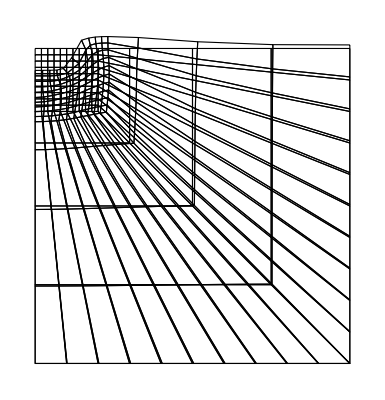

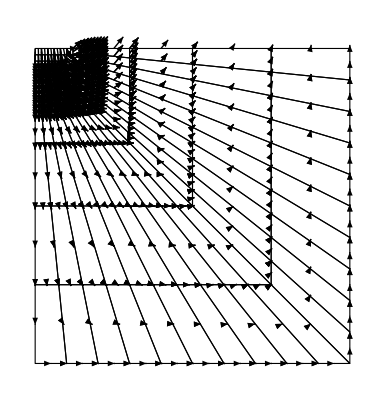

Part::partw: Part 6 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 6⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification 6.⟦1⟧ is longer than depth of object.

Part::partd: Part specification 6.⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6.⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

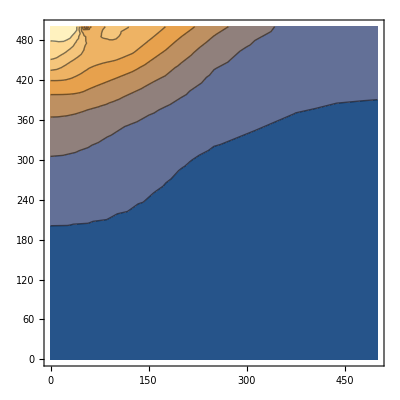

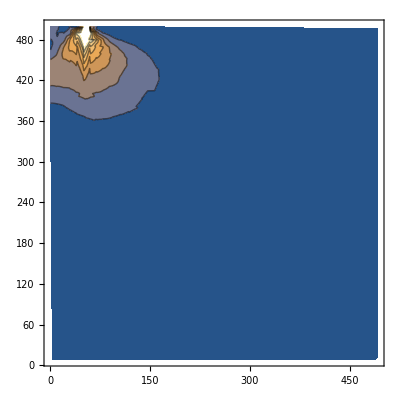

```mathematica
solu=6;
sol=solss[[solu]];
scale=200;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]


{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Arrowheads[.02],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
sh=Show[meshVis1,arrows,PlotRange->All]

teste1=Table[{dgammasol[[solu]][[i]][[1]],dgammasol[[solu]][[i]][[2]],dgammasol[[solu]][[i]][[3]]},{i,1,Length[dgammasol[[solu]]]}];
Show[ListContourPlot[teste1,PlotLegends->{Placed[Automatic,{Right,Center}]}],PlotRange->All,AspectRatio->Automatic,Frame->False]
ListContourPlot[vecs3]
(*show[{{0,340},{160,515}},sh]*)

tab=Table[{epspsolu[[solu]][[i]][[1]],epspsolu[[solu]][[i]][[2]],Norm[epspsolu[[solu]][[i]][[3]]]},{i,1,Length[epspsolu[[solu]]]}];
ListContourPlot[tab]


(*tab=Table[{stresssolu[[solu]][[i]][[1]],stresssolu[[solu]][[i]][[2]],stresssolu[[solu]][[i]][[3]][[3]]},{i,1,Length[stresssolu[[solu]]]}];
ListContourPlot[tab]*)
(*show[{{0,350},{150,510}},g]*)
```

```mathematica
sol2={{0,0},{0.00008090567106165366,1.5000000000000002},{0.00024271704466403147,4.5},{0.0005432577908282163,9.},{0.0006840245828463058,10.500000000000002},{0.0008480191616594057,12.000000000000002},{0.0009041108974141578,12.375000000000002},{0.0009566657492336292,12.750000000000002},{0.001010936568401989,13.125000000000002},{0.0010705349467467215,13.500000000000002},{0.001200057577611607,14.250000000000002}}
```

{{0,0},{0.0000809057,1.5},{0.000242717,4.5},{0.000543258,9.},{0.000684025,10.5},{0.000848019,12.},{0.000904111,12.375},{0.000956666,12.75},{0.00101094,13.125},{0.00107053,13.5},{0.00120006,14.25}}

```mathematica
sol2
```

{{0,0},{0.0000809044,1.5},{0.000242714,4.5},{0.00054087,9.},{0.000680081,10.5},{0.000842789,12.},{0.0010454,13.5},{0.00118641,14.25},{0.00142028,15.},{0.00161844,15.15},{0.00180859,15.225}}

```mathematica
sol2
```

{{0,0},{0.0000809044,1.5},{0.000242714,4.5},{0.00054087,9.},{0.000680081,10.5},{0.000842789,12.},{0.0010454,13.5},{0.00118641,14.25},{0.00142028,15.},{0.00161844,15.15},{0.00180859,15.225},{0.00201056,15.3},{0.00223768,15.375},{0.00249614,15.45},{0.00279437,15.465},{0.00297219,15.48}}

```mathematica
fourpoinr={{0,0},{0.00008090434474277526,1.5000000000000002},{0.00024271344781272246,4.5},{0.0005407311160259379,9.},{0.0006799451701411358,10.500000000000002},{0.0008427477795692027,12.000000000000002},{0.0010447756026585769,13.500000000000002},{0.001185191949634557,14.250000000000002},{0.0014220597897036482,15.000000000000002},{0.0016208750759519447,15.150000000000002},{0.0018127617462285611,15.225}}
```

{{0,0},{0.0000809043,1.5},{0.000242713,4.5},{0.000540731,9.},{0.000679945,10.5},{0.000842748,12.},{0.00104478,13.5},{0.00118519,14.25},{0.00142206,15.},{0.00162088,15.15},{0.00181276,15.225}}

```mathematica
1.03 15
```

15.45

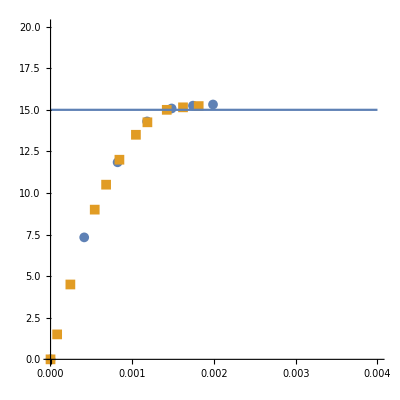

```mathematica
Show[ListPlot[{sol2,fourpoinr},AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[15.,{x,0,0.004}],PlotRange->{{0,0.004},{0,20}}]
```

{{6.66667,40.},{6.66667,35.8941},{10.,36.25},{10.,40.},{6.66667,37.9546},{8.33333,36.1176},{10.,38.125},{8.33333,40.}}

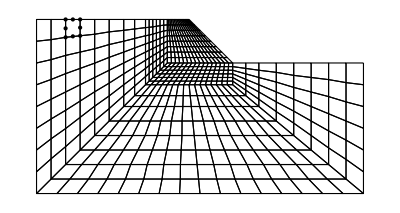

2

{1,2,5,12,17,26,35,48,64,79,100,123,149,178,209,243,278,319,381,466,563,668,803,950,1119,1278,1378,1435,1471,1501,1526,1550,1571}

{1571,1572,1574,1577,1579,1581,1586,1588,1591,1596,1599,1602,1605,1608,1610,1612,1613}

{1,3,6,13,18,29,39,55,70,91,112,139,170}

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mypaper\\mesh-talude-els.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mypaper\\mesh-talude-nodes.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];

meshVis2=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
el=1;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]

order=2
serendipity=True;

x0=0.;xf=75;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=40;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=75;xf=75;
y0=0;yf=30;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


subst2={c->50.,phi->20/180. Pi,young->20000. (*kPa*),nu->0.49,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),A->3 Tan[phi]/Sqrt[9+12 Tan[phi]^2],
B->3 /Sqrt[9+12 Tan[phi]^2]};


f[x_]:=0;
(*FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];*)
bodyforce=20;


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};
soltalude={};
lamb=1;
diff=10;
l0=3.;
l=l0
niterdesired=5;
counterout=1;
tol1=10^-3;
tol2=10^-6;
While[Abs[diff]>tol1 && counterout≤30,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol2,

epsppost={};
dgamma={};
stressppost={};
globalcounter=1;
{KT,FINT,FEXTB}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
FEXT=FEXTB;
imposex=1;
imposey=2;
R=lamb  FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsinferior,{imposey,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsleft,{imposex,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];;
aa=dwb.dwb;
bb=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
(*Print["a = ",aa];
Print["b = ",bb];
Print["c = ",ccc];*)
dlamb=Solve[aa x^2 +bb x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];

Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[lamb FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb, " | bodyforce lamb = ",bodyforce lamb];
counter++;
];
diff=Abs[lamb-lambn];
l=l0 niterdesired/counter;
Print["l = ",l];
AppendTo[stresssolu,stressppost];
AppendTo[dgammasol,dgamma];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];
id=FindIds[nnodes,{{35,40}}][[1]];
AppendTo[soltalude,{-displace[[id 2]], lamb}];
AppendTo[sol3,epspvec];

(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

3.

i = 1 | lamb = 1 | lambn = 3.63326 | diff = 10

Iteration number = 1  |R|/|FE| =  1.52856  |Δu|/|u| = 1.  |R| =  3252.58 |dw| = 3. | dlamb = -0.345791 | lamb = 0.654209 | bodyforce lamb = 13.0842

Iteration number = 2  |R|/|FE| =  0.00712223  |Δu|/|u| = 0.0000378736  |R| =  15.155 |dw| = 0.000113621 | dlamb = -8.2765×10^-6 | lamb = 0.6542 | bodyforce lamb = 13.084

Iteration number = 3  |R|/|FE| =  4.26224×10^-6  |Δu|/|u| = 4.9854×10^-8  |R| =  0.00906938 |dw| = 1.49562×10^-7 | dlamb = -2.00388×10^-9 | lamb = 0.6542 | bodyforce lamb = 13.084

l = 3.75

i = 2 | lamb = 0.6542 | lambn = 1 | diff = 0.3458

Iteration number = 1  |R|/|FE| =  0.0000279037  |Δu|/|u| = 0.555556  |R| =  0.133591 |dw| = 3.75 | dlamb = 0.817722 | lamb = 1.47192 | bodyforce lamb = 29.4385

Iteration number = 2  |R|/|FE| =  0.0295745  |Δu|/|u| = 0.000893253  |R| =  141.529 |dw| = 0.00602946 | dlamb = -0.000630997 | lamb = 1.47129 | bodyforce lamb = 29.4258

Iteration number = 3  |R|/|FE| =  0.0205106  |Δu|/|u| = 0.00137895  |R| =  98.0908 |dw| = 0.00930791 | dlamb = -0.000938748 | lamb = 1.47035 | bodyforce lamb = 29.4071

Iteration number = 4  |R|/|FE| =  0.0337252  |Δu|/|u| = 0.000212248  |R| =  161.277 |dw| = 0.00143267 | dlamb = -0.000112942 | lamb = 1.47024 | bodyforce lamb = 29.4048

Iteration number = 5  |R|/|FE| =  0.00498919  |Δu|/|u| = 0.0000432343  |R| =  23.8583 |dw| = 0.000291831 | dlamb = -0.0000254563 | lamb = 1.47021 | bodyforce lamb = 29.4043

Iteration number = 6  |R|/|FE| =  0.000725454  |Δu|/|u| = 6.15028×10^-6  |R| =  3.46911 |dw| = 0.0000415143 | dlamb = -2.52489×10^-6 | lamb = 1.47021 | bodyforce lamb = 29.4042

Iteration number = 7  |R|/|FE| =  3.23143×10^-7  |Δu|/|u| = 3.78552×10^-9  |R| =  0.00154527 |dw| = 2.55522×10^-8 | dlamb = -1.88831×10^-9 | lamb = 1.47021 | bodyforce lamb = 29.4042

l = 1.875

i = 3 | lamb = 1.47021 | lambn = 0.6542 | diff = 0.816012

Iteration number = 1  |R|/|FE| =  0.00147034  |Δu|/|u| = 0.217394  |R| =  8.9742 |dw| = 1.875 | dlamb = 0.406291 | lamb = 1.8765 | bodyforce lamb = 37.5301

Iteration number = 2  |R|/|FE| =  0.0122273  |Δu|/|u| = 0.000930317  |R| =  74.5934 |dw| = 0.00802382 | dlamb = -0.000897268 | lamb = 1.87561 | bodyforce lamb = 37.5121

Iteration number = 3  |R|/|FE| =  0.00670133  |Δu|/|u| = 0.000295998  |R| =  40.8765 |dw| = 0.00255292 | dlamb = -0.000246089 | lamb = 1.87536 | bodyforce lamb = 37.5072

Iteration number = 4  |R|/|FE| =  0.00295792  |Δu|/|u| = 0.0000740526  |R| =  18.0421 |dw| = 0.000638688 | dlamb = -0.0000531737 | lamb = 1.87531 | bodyforce lamb = 37.5061

Iteration number = 5  |R|/|FE| =  0.00133505  |Δu|/|u| = 0.0000183663  |R| =  8.14319 |dw| = 0.000158406 | dlamb = -0.0000104826 | lamb = 1.8753 | bodyforce lamb = 37.5059

Iteration number = 6  |R|/|FE| =  8.79791×10^-7  |Δu|/|u| = 4.38764×10^-8  |R| =  0.00536634 |dw| = 3.78425×10^-7 | dlamb = -3.34534×10^-8 | lamb = 1.8753 | bodyforce lamb = 37.5059

l = 2.14286

i = 4 | lamb = 1.8753 | lambn = 1.47021 | diff = 0.405084

Iteration number = 1  |R|/|FE| =  0.00150846  |Δu|/|u| = 0.199013  |R| =  11.4679 |dw| = 2.14286 | dlamb = 0.462047 | lamb = 2.33734 | bodyforce lamb = 46.7469

Iteration number = 2  |R|/|FE| =  0.0263411  |Δu|/|u| = 0.00201644  |R| =  200.021 |dw| = 0.0217111 | dlamb = -0.00274169 | lamb = 2.3346 | bodyforce lamb = 46.692

Iteration number = 3  |R|/|FE| =  0.0127822  |Δu|/|u| = 0.000510134  |R| =  97.0337 |dw| = 0.00549258 | dlamb = -0.000664803 | lamb = 2.33394 | bodyforce lamb = 46.6787

Iteration number = 4  |R|/|FE| =  0.00392355  |Δu|/|u| = 0.00013048  |R| =  29.7834 |dw| = 0.00140487 | dlamb = -0.000118395 | lamb = 2.33382 | bodyforce lamb = 46.6764

Iteration number = 5  |R|/|FE| =  0.000377782  |Δu|/|u| = 3.622×10^-6  |R| =  2.86771 |dw| = 0.0000389978 | dlamb = -3.06582×10^-6 | lamb = 2.33381 | bodyforce lamb = 46.6763

Iteration number = 6  |R|/|FE| =  9.81819×10^-7  |Δu|/|u| = 3.10649×10^-9  |R| =  0.00745291 |dw| = 3.34473×10^-8 | dlamb = -2.59172×10^-9 | lamb = 2.33381 | bodyforce lamb = 46.6763

l = 2.14286

i = 5 | lamb = 2.33381 | lambn = 1.8753 | diff = 0.458519

Iteration number = 1  |R|/|FE| =  0.00172237  |Δu|/|u| = 0.165996  |R| =  15.63 |dw| = 2.14286 | dlamb = 0.45618 | lamb = 2.78999 | bodyforce lamb = 55.7999

Iteration number = 2  |R|/|FE| =  0.0227927  |Δu|/|u| = 0.00261554  |R| =  206.463 |dw| = 0.0337617 | dlamb = -0.00503973 | lamb = 2.78495 | bodyforce lamb = 55.6991

Iteration number = 3  |R|/|FE| =  0.00726768  |Δu|/|u| = 0.00051699  |R| =  65.816 |dw| = 0.00667325 | dlamb = -0.000710433 | lamb = 2.78424 | bodyforce lamb = 55.6849

Iteration number = 4  |R|/|FE| =  0.00236325  |Δu|/|u| = 0.0000554271  |R| =  21.4011 |dw| = 0.000715446 | dlamb = -0.0000706481 | lamb = 2.78417 | bodyforce lamb = 55.6835

Iteration number = 5  |R|/|FE| =  0.00113642  |Δu|/|u| = 0.0000221394  |R| =  10.2911 |dw| = 0.000285772 | dlamb = -0.0000219304 | lamb = 2.78415 | bodyforce lamb = 55.683

Iteration number = 6  |R|/|FE| =  1.73745×10^-6  |Δu|/|u| = 8.85704×10^-8  |R| =  0.0157338 |dw| = 1.14325×10^-6 | dlamb = -8.1012×10^-8 | lamb = 2.78415 | bodyforce lamb = 55.683

l = 2.14286

i = 6 | lamb = 2.78415 | lambn = 2.33381 | diff = 0.450337

Iteration number = 1  |R|/|FE| =  0.00227557  |Δu|/|u| = 0.14239  |R| =  23.9301 |dw| = 2.14286 | dlamb = 0.448999 | lamb = 3.23315 | bodyforce lamb = 64.663

Iteration number = 2  |R|/|FE| =  0.0223369  |Δu|/|u| = 0.00323112  |R| =  234.387 |dw| = 0.0486192 | dlamb = -0.00703025 | lamb = 3.22612 | bodyforce lamb = 64.5224

Iteration number = 3  |R|/|FE| =  0.0082952  |Δu|/|u| = 0.000860236  |R| =  87.0072 |dw| = 0.0129435 | dlamb = -0.00134285 | lamb = 3.22478 | bodyforce lamb = 64.4955

Iteration number = 4  |R|/|FE| =  0.00273712  |Δu|/|u| = 0.000177307  |R| =  28.7071 |dw| = 0.00266782 | dlamb = -0.000243783 | lamb = 3.22453 | bodyforce lamb = 64.4907

Iteration number = 5  |R|/|FE| =  0.000792429  |Δu|/|u| = 0.000031681  |R| =  8.31095 |dw| = 0.000476683 | dlamb = -0.0000380295 | lamb = 3.2245 | bodyforce lamb = 64.4899

Iteration number = 6  |R|/|FE| =  0.000384594  |Δu|/|u| = 0.0000111843  |R| =  4.03358 |dw| = 0.000168283 | dlamb = -0.0000129881 | lamb = 3.22448 | bodyforce lamb = 64.4897

Iteration number = 7  |R|/|FE| =  1.33599×10^-7  |Δu|/|u| = 2.26316×10^-8  |R| =  0.00140118 |dw| = 3.40523×10^-7 | dlamb = -3.24161×10^-8 | lamb = 3.22448 | bodyforce lamb = 64.4897

l = 1.875

i = 7 | lamb = 3.22448 | lambn = 2.78415 | diff = 0.440331

Iteration number = 1  |R|/|FE| =  0.00271515  |Δu|/|u| = 0.110823  |R| =  31.8816 |dw| = 1.875 | dlamb = 0.385593 | lamb = 3.61008 | bodyforce lamb = 72.2015

Iteration number = 2  |R|/|FE| =  0.0105237  |Δu|/|u| = 0.00389317  |R| =  123.311 |dw| = 0.065852 | dlamb = -0.00757508 | lamb = 3.6025 | bodyforce lamb = 72.05

Iteration number = 3  |R|/|FE| =  0.00632751  |Δu|/|u| = 0.00101797  |R| =  74.1057 |dw| = 0.0172173 | dlamb = -0.00177457 | lamb = 3.60073 | bodyforce lamb = 72.0145

Iteration number = 4  |R|/|FE| =  0.00317182  |Δu|/|u| = 0.000337015  |R| =  37.1413 |dw| = 0.00569993 | dlamb = -0.000587676 | lamb = 3.60014 | bodyforce lamb = 72.0028

Iteration number = 5  |R|/|FE| =  0.00155113  |Δu|/|u| = 0.0000581384  |R| =  18.1628 |dw| = 0.000983291 | dlamb = -0.00010299 | lamb = 3.60004 | bodyforce lamb = 72.0007

Iteration number = 6  |R|/|FE| =  0.000082813  |Δu|/|u| = 5.97063×10^-6  |R| =  0.969689 |dw| = 0.000100981 | dlamb = -9.66605×10^-6 | lamb = 3.60003 | bodyforce lamb = 72.0005

Iteration number = 7  |R|/|FE| =  2.21401×10^-6  |Δu|/|u| = 9.63585×10^-7  |R| =  0.0259247 |dw| = 0.000016297 | dlamb = -1.42882×10^-6 | lamb = 3.60002 | bodyforce lamb = 72.0005

l = 1.875

i = 8 | lamb = 3.60002 | lambn = 3.22448 | diff = 0.375541

Iteration number = 1  |R|/|FE| =  0.00290681  |Δu|/|u| = 0.0998191  |R| =  37.6358 |dw| = 1.875 | dlamb = 0.380651 | lamb = 3.98067 | bodyforce lamb = 79.6135

Iteration number = 2  |R|/|FE| =  0.00961059  |Δu|/|u| = 0.00610575  |R| =  124.027 |dw| = 0.11463 | dlamb = -0.0129716 | lamb = 3.9677 | bodyforce lamb = 79.3541

Iteration number = 3  |R|/|FE| =  0.0115095  |Δu|/|u| = 0.00166255  |R| =  148.404 |dw| = 0.0312069 | dlamb = -0.00347655 | lamb = 3.96423 | bodyforce lamb = 79.2845

Iteration number = 4  |R|/|FE| =  0.00357369  |Δu|/|u| = 0.000610534  |R| =  46.0645 |dw| = 0.0114591 | dlamb = -0.00126171 | lamb = 3.96296 | bodyforce lamb = 79.2593

Iteration number = 5  |R|/|FE| =  0.00112976  |Δu|/|u| = 0.000246816  |R| =  14.5606 |dw| = 0.00463238 | dlamb = -0.000512617 | lamb = 3.96245 | bodyforce lamb = 79.249

Iteration number = 6  |R|/|FE| =  0.000218837  |Δu|/|u| = 0.0000883685  |R| =  2.82029 |dw| = 0.00165853 | dlamb = -0.000171277 | lamb = 3.96228 | bodyforce lamb = 79.2456

Iteration number = 7  |R|/|FE| =  0.0000531972  |Δu|/|u| = 0.0000414896  |R| =  0.685573 |dw| = 0.000778689 | dlamb = -0.000080127 | lamb = 3.9622 | bodyforce lamb = 79.244

Iteration number = 8  |R|/|FE| =  0.0000253414  |Δu|/|u| = 0.0000196527  |R| =  0.326581 |dw| = 0.000368846 | dlamb = -0.0000379909 | lamb = 3.96216 | bodyforce lamb = 79.2433

Iteration number = 9  |R|/|FE| =  0.0000119539  |Δu|/|u| = 9.288×10^-6  |R| =  0.154052 |dw| = 0.000174319 | dlamb = -0.0000179511 | lamb = 3.96214 | bodyforce lamb = 79.2429

Iteration number = 10  |R|/|FE| =  5.65479×10^-6  |Δu|/|u| = 4.39091×10^-6  |R| =  0.0728743 |dw| = 0.0000824095 | dlamb = -8.48696×10^-6 | lamb = 3.96214 | bodyforce lamb = 79.2427

Iteration number = 11  |R|/|FE| =  2.67376×10^-6  |Δu|/|u| = 2.07553×10^-6  |R| =  0.0344572 |dw| = 0.000038954 | dlamb = -4.01181×10^-6 | lamb = 3.96213 | bodyforce lamb = 79.2426

Iteration number = 12  |R|/|FE| =  1.26395×10^-6  |Δu|/|u| = 9.81018×10^-7  |R| =  0.0162888 |dw| = 0.000018412 | dlamb = -1.89624×10^-6 | lamb = 3.96213 | bodyforce lamb = 79.2426

l = 1.15385

i = 9 | lamb = 3.96213 | lambn = 3.60002 | diff = 0.362107

Iteration number = 1  |R|/|FE| =  0.00421322  |Δu|/|u| = 0.0579357  |R| =  57.4218 |dw| = 1.15385 | dlamb = 0.22806 | lamb = 4.19019 | bodyforce lamb = 83.8038

Iteration number = 2  |R|/|FE| =  0.00627933  |Δu|/|u| = 0.0056866  |R| =  85.309 |dw| = 0.113162 | dlamb = -0.013298 | lamb = 4.17689 | bodyforce lamb = 83.5379

Iteration number = 3  |R|/|FE| =  0.00435875  |Δu|/|u| = 0.00191489  |R| =  59.1504 |dw| = 0.0380912 | dlamb = -0.00466815 | lamb = 4.17222 | bodyforce lamb = 83.4445

Iteration number = 4  |R|/|FE| =  0.00244273  |Δu|/|u| = 0.00116447  |R| =  33.126 |dw| = 0.0231583 | dlamb = -0.00291348 | lamb = 4.16931 | bodyforce lamb = 83.3862

Iteration number = 5  |R|/|FE| =  0.000962288  |Δu|/|u| = 0.000737207  |R| =  13.0438 |dw| = 0.0146591 | dlamb = -0.00185439 | lamb = 4.16746 | bodyforce lamb = 83.3491

Iteration number = 6  |R|/|FE| =  0.000488219  |Δu|/|u| = 0.000440707  |R| =  6.61599 |dw| = 0.00876249 | dlamb = -0.00114176 | lamb = 4.16632 | bodyforce lamb = 83.3263

Iteration number = 7  |R|/|FE| =  0.000235396  |Δu|/|u| = 0.000237662  |R| =  3.18944 |dw| = 0.00472515 | dlamb = -0.00062286 | lamb = 4.16569 | bodyforce lamb = 83.3138

Iteration number = 8  |R|/|FE| =  0.000119687  |Δu|/|u| = 0.000122802  |R| =  1.62154 |dw| = 0.00244145 | dlamb = -0.000323574 | lamb = 4.16537 | bodyforce lamb = 83.3074

Iteration number = 9  |R|/|FE| =  0.0000561035  |Δu|/|u| = 0.0000610839  |R| =  0.760073 |dw| = 0.00121441 | dlamb = -0.000161089 | lamb = 4.16521 | bodyforce lamb = 83.3042

Iteration number = 10  |R|/|FE| =  0.0000282788  |Δu|/|u| = 0.0000307951  |R| =  0.383105 |dw| = 0.000612233 | dlamb = -0.000081312 | lamb = 4.16513 | bodyforce lamb = 83.3025

Iteration number = 11  |R|/|FE| =  0.0000142629  |Δu|/|u| = 0.0000155536  |R| =  0.193223 |dw| = 0.000309218 | dlamb = -0.0000411113 | lamb = 4.16509 | bodyforce lamb = 83.3017

Iteration number = 12  |R|/|FE| =  7.133×10^-6  |Δu|/|u| = 7.79412×10^-6  |R| =  0.0966324 |dw| = 0.000154953 | dlamb = -0.0000206028 | lamb = 4.16506 | bodyforce lamb = 83.3013

Iteration number = 13  |R|/|FE| =  3.58082×10^-6  |Δu|/|u| = 3.91247×10^-6  |R| =  0.04851 |dw| = 0.0000777828 | dlamb = -0.0000103436 | lamb = 4.16505 | bodyforce lamb = 83.3011

Iteration number = 14  |R|/|FE| =  1.79719×10^-6  |Δu|/|u| = 1.96359×10^-6  |R| =  0.0243469 |dw| = 0.0000390377 | dlamb = -5.1916×10^-6 | lamb = 4.16505 | bodyforce lamb = 83.301

Iteration number = 15  |R|/|FE| =  9.01897×10^-7  |Δu|/|u| = 9.85389×10^-7  |R| =  0.0122181 |dw| = 0.0000195902 | dlamb = -2.60539×10^-6 | lamb = 4.16505 | bodyforce lamb = 83.3009

l = 0.9375

i = 10 | lamb = 4.16505 | lambn = 3.96213 | diff = 0.202916

Iteration number = 1  |R|/|FE| =  0.00627736  |Δu|/|u| = 0.0450553  |R| =  88.7132 |dw| = 0.9375 | dlamb = 0.179881 | lamb = 4.34493 | bodyforce lamb = 86.8986

Iteration number = 2  |R|/|FE| =  0.00572528  |Δu|/|u| = 0.0119309  |R| =  80.3213 |dw| = 0.247468 | dlamb = -0.0316746 | lamb = 4.31325 | bodyforce lamb = 86.2651

Iteration number = 3  |R|/|FE| =  0.00615541  |Δu|/|u| = 0.00996953  |R| =  85.6987 |dw| = 0.205804 | dlamb = -0.0328051 | lamb = 4.28045 | bodyforce lamb = 85.609

Iteration number = 4  |R|/|FE| =  0.00498717  |Δu|/|u| = 0.00280325  |R| =  69.2653 |dw| = 0.0577731 | dlamb = -0.0103982 | lamb = 4.27005 | bodyforce lamb = 85.401

Iteration number = 5  |R|/|FE| =  0.001228  |Δu|/|u| = 0.000909093  |R| =  17.0417 |dw| = 0.0187266 | dlamb = -0.00341232 | lamb = 4.26664 | bodyforce lamb = 85.3327

Iteration number = 6  |R|/|FE| =  0.000816128  |Δu|/|u| = 0.00104156  |R| =  11.3157 |dw| = 0.0214437 | dlamb = -0.00385466 | lamb = 4.26278 | bodyforce lamb = 85.2557

Iteration number = 7  |R|/|FE| =  0.000678745  |Δu|/|u| = 0.00100433  |R| =  9.4024 |dw| = 0.0206656 | dlamb = -0.00382121 | lamb = 4.25896 | bodyforce lamb = 85.1792

Iteration number = 8  |R|/|FE| =  0.00346592  |Δu|/|u| = 0.000783555  |R| =  47.9774 |dw| = 0.0161155 | dlamb = -0.0030771 | lamb = 4.25588 | bodyforce lamb = 85.1177

Iteration number = 9  |R|/|FE| =  0.000308536  |Δu|/|u| = 0.000577861  |R| =  4.26865 |dw| = 0.0118809 | dlamb = -0.00228767 | lamb = 4.2536 | bodyforce lamb = 85.0719

Iteration number = 10  |R|/|FE| =  0.000202449  |Δu|/|u| = 0.000392245  |R| =  2.79989 |dw| = 0.00806267 | dlamb = -0.00156534 | lamb = 4.25203 | bodyforce lamb = 85.0406

Iteration number = 11  |R|/|FE| =  0.000129916  |Δu|/|u| = 0.000258616  |R| =  1.79631 |dw| = 0.00531505 | dlamb = -0.00103711 | lamb = 4.25099 | bodyforce lamb = 85.0199

Iteration number = 12  |R|/|FE| =  0.0000828503  |Δu|/|u| = 0.0001681  |R| =  1.14537 |dw| = 0.00345441 | dlamb = -0.000676149 | lamb = 4.25032 | bodyforce lamb = 85.0064

Iteration number = 13  |R|/|FE| =  0.0000530275  |Δu|/|u| = 0.000108429  |R| =  0.733005 |dw| = 0.00222803 | dlamb = -0.000436965 | lamb = 4.24988 | bodyforce lamb = 84.9976

Iteration number = 14  |R|/|FE| =  0.0000338976  |Δu|/|u| = 0.0000696222  |R| =  0.468539 |dw| = 0.00143056 | dlamb = -0.000280934 | lamb = 4.2496 | bodyforce lamb = 84.992

Iteration number = 15  |R|/|FE| =  0.0000216402  |Δu|/|u| = 0.0000445867  |R| =  0.299102 |dw| = 0.000916118 | dlamb = -0.000180042 | lamb = 4.24942 | bodyforce lamb = 84.9884

Iteration number = 16  |R|/|FE| =  0.0000138155  |Δu|/|u| = 0.0000285115  |R| =  0.190947 |dw| = 0.000585813 | dlamb = -0.000115187 | lamb = 4.24931 | bodyforce lamb = 84.9861

Iteration number = 17  |R|/|FE| =  8.81113×10^-6  |Δu|/|u| = 0.0000182096  |R| =  0.121778 |dw| = 0.000374139 | dlamb = -0.0000735893 | lamb = 4.24923 | bodyforce lamb = 84.9846

Iteration number = 18  |R|/|FE| =  5.62022×10^-6  |Δu|/|u| = 0.0000116235  |R| =  0.0776761 |dw| = 0.000238818 | dlamb = -0.0000469825 | lamb = 4.24918 | bodyforce lamb = 84.9837

Iteration number = 19  |R|/|FE| =  3.58442×10^-6  |Δu|/|u| = 7.41652×10^-6  |R| =  0.0495393 |dw| = 0.00015238 | dlamb = -0.0000299816 | lamb = 4.24915 | bodyforce lamb = 84.9831

Iteration number = 20  |R|/|FE| =  2.28585×10^-6  |Δu|/|u| = 4.73103×10^-6  |R| =  0.0315919 |dw| = 0.0000972037 | dlamb = -0.0000191269 | lamb = 4.24914 | bodyforce lamb = 84.9827

Iteration number = 21  |R|/|FE| =  1.45765×10^-6  |Δu|/|u| = 3.01746×10^-6  |R| =  0.0201456 |dw| = 0.0000619966 | dlamb = -0.0000121998 | lamb = 4.24912 | bodyforce lamb = 84.9825

Iteration number = 22  |R|/|FE| =  9.29488×10^-7  |Δu|/|u| = 1.92435×10^-6  |R| =  0.0128461 |dw| = 0.0000395376 | dlamb = -7.78053×10^-6 | lamb = 4.24912 | bodyforce lamb = 84.9823

Iteration number = 23  |R|/|FE| =  5.92687×10^-7  |Δu|/|u| = 1.22715×10^-6  |R| =  0.00819128 |dw| = 0.000025213 | dlamb = -4.96172×10^-6 | lamb = 4.24911 | bodyforce lamb = 84.9822

Iteration number = 24  |R|/|FE| =  3.77921×10^-7  |Δu|/|u| = 7.8252×10^-7  |R| =  0.00522309 |dw| = 0.0000160776 | dlamb = -3.16399×10^-6 | lamb = 4.24911 | bodyforce lamb = 84.9821

l = 0.6

i = 11 | lamb = 4.24911 | lambn = 4.16505 | diff = 0.0840608

Iteration number = 1  |R|/|FE| =  0.00939603  |Δu|/|u| = 0.0283877  |R| =  133.289 |dw| = 0.6 | dlamb = 0.112259 | lamb = 4.36137 | bodyforce lamb = 87.2273

Iteration number = 2  |R|/|FE| =  0.0259014  |Δu|/|u| = 0.010177  |R| =  364.777 |dw| = 0.214348 | dlamb = -0.0314958 | lamb = 4.32987 | bodyforce lamb = 86.5974

Iteration number = 3  |R|/|FE| =  0.00514494  |Δu|/|u| = 0.00883705  |R| =  71.8823 |dw| = 0.185109 | dlamb = -0.0343728 | lamb = 4.2955 | bodyforce lamb = 85.91

Iteration number = 4  |R|/|FE| =  0.00399263  |Δu|/|u| = 0.00398199  |R| =  55.5631 |dw| = 0.0831553 | dlamb = -0.0169186 | lamb = 4.27858 | bodyforce lamb = 85.5716

Iteration number = 5  |R|/|FE| =  0.00086241  |Δu|/|u| = 0.000433757  |R| =  11.9965 |dw| = 0.00905491 | dlamb = -0.00184679 | lamb = 4.27673 | bodyforce lamb = 85.5346

Iteration number = 6  |R|/|FE| =  0.000131097  |Δu|/|u| = 0.0000108706  |R| =  1.82359 |dw| = 0.000226929 | dlamb = -0.0000498854 | lamb = 4.27668 | bodyforce lamb = 85.5336

Iteration number = 7  |R|/|FE| =  0.0000100117  |Δu|/|u| = 5.21793×10^-7  |R| =  0.139265 |dw| = 0.0000108926 | dlamb = -1.78235×10^-6 | lamb = 4.27668 | bodyforce lamb = 85.5336

l = 1.875

i = 12 | lamb = 4.27668 | lambn = 4.24911 | diff = 0.0275731

Iteration number = 1  |R|/|FE| =  0.00186562  |Δu|/|u| = 0.0824249  |R| =  28.2157 |dw| = 1.875 | dlamb = 0.373167 | lamb = 4.64985 | bodyforce lamb = 92.9969

Iteration number = 2  |R|/|FE| =  0.0561058  |Δu|/|u| = 0.0322796  |R| =  830.77 |dw| = 0.729095 | dlamb = -0.0974023 | lamb = 4.55245 | bodyforce lamb = 91.0489

Iteration number = 3  |R|/|FE| =  0.0160644  |Δu|/|u| = 0.0301307  |R| =  231.517 |dw| = 0.669719 | dlamb = -0.121566 | lamb = 4.43088 | bodyforce lamb = 88.6176

Iteration number = 4  |R|/|FE| =  0.0342888  |Δu|/|u| = 0.0131741  |R| =  488.469 |dw| = 0.290324 | dlamb = -0.0510617 | lamb = 4.37982 | bodyforce lamb = 87.5964

Iteration number = 5  |R|/|FE| =  0.0114886  |Δu|/|u| = 0.00867908  |R| =  162.411 |dw| = 0.190094 | dlamb = -0.0335067 | lamb = 4.34631 | bodyforce lamb = 86.9262

Iteration number = 6  |R|/|FE| =  0.00625346  |Δu|/|u| = 0.00158392  |R| =  88.2589 |dw| = 0.0346482 | dlamb = -0.00711166 | lamb = 4.3392 | bodyforce lamb = 86.784

Iteration number = 7  |R|/|FE| =  0.00132699  |Δu|/|u| = 0.0000841641  |R| =  18.7273 |dw| = 0.00184098 | dlamb = -0.000325786 | lamb = 4.33887 | bodyforce lamb = 86.7775

Iteration number = 8  |R|/|FE| =  0.000108832  |Δu|/|u| = 3.33893×10^-6  |R| =  1.53589 |dw| = 0.0000730346 | dlamb = -0.0000110781 | lamb = 4.33886 | bodyforce lamb = 86.7772

Iteration number = 9  |R|/|FE| =  1.83093×10^-7  |Δu|/|u| = 9.04997×10^-9  |R| =  0.0025839 |dw| = 1.97956×10^-7 | dlamb = -2.11527×10^-8 | lamb = 4.33886 | bodyforce lamb = 86.7772

l = 1.5

i = 13 | lamb = 4.33886 | lambn = 4.27668 | diff = 0.062182

Iteration number = 1  |R|/|FE| =  0.00229836  |Δu|/|u| = 0.0641929  |R| =  34.516 |dw| = 1.5 | dlamb = 0.278285 | lamb = 4.61715 | bodyforce lamb = 92.3429

Iteration number = 2  |R|/|FE| =  0.0112556  |Δu|/|u| = 0.0426351  |R| =  162.984 |dw| = 0.980016 | dlamb = -0.16521 | lamb = 4.45194 | bodyforce lamb = 89.0388

Iteration number = 3  |R|/|FE| =  0.00480327  |Δu|/|u| = 0.022381  |R| =  67.9513 |dw| = 0.505918 | dlamb = -0.102508 | lamb = 4.34943 | bodyforce lamb = 86.9886

Iteration number = 4  |R|/|FE| =  0.00826533  |Δu|/|u| = 0.000842811  |R| =  116.815 |dw| = 0.0190384 | dlamb = -0.00421856 | lamb = 4.34521 | bodyforce lamb = 86.9042

Iteration number = 5  |R|/|FE| =  0.000850866  |Δu|/|u| = 0.0000455198  |R| =  12.0253 |dw| = 0.00102826 | dlamb = -0.0000477911 | lamb = 4.34516 | bodyforce lamb = 86.9033

Iteration number = 6  |R|/|FE| =  0.0000677136  |Δu|/|u| = 2.41711×10^-6  |R| =  0.956997 |dw| = 0.0000546007 | dlamb = 3.8835×10^-8 | lamb = 4.34516 | bodyforce lamb = 86.9033

Iteration number = 7  |R|/|FE| =  1.26573×10^-8  |Δu|/|u| = 1.27201×10^-9  |R| =  0.000178885 |dw| = 2.87337×10^-8 | dlamb = -1.57559×10^-9 | lamb = 4.34516 | bodyforce lamb = 86.9033

l = 1.875

i = 14 | lamb = 4.34516 | lambn = 4.33886 | diff = 0.00630138

Iteration number = 1  |R|/|FE| =  0.00220902  |Δu|/|u| = 0.0766465  |R| =  33.7428 |dw| = 1.875 | dlamb = 0.351106 | lamb = 4.69627 | bodyforce lamb = 93.9254

Iteration number = 2  |R|/|FE| =  0.0103484  |Δu|/|u| = 0.0532716  |R| =  150.792 |dw| = 1.28032 | dlamb = -0.216299 | lamb = 4.47997 | bodyforce lamb = 89.5994

Iteration number = 3  |R|/|FE| =  0.00662769  |Δu|/|u| = 0.0253574  |R| =  93.9903 |dw| = 0.598641 | dlamb = -0.119916 | lamb = 4.36006 | bodyforce lamb = 87.2011

Iteration number = 4  |R|/|FE| =  0.0127243  |Δu|/|u| = 0.000886952  |R| =  180.263 |dw| = 0.0209259 | dlamb = -0.00447875 | lamb = 4.35558 | bodyforce lamb = 87.1115

Iteration number = 5  |R|/|FE| =  0.00129506  |Δu|/|u| = 0.0000915388  |R| =  18.3467 |dw| = 0.0021597 | dlamb = -0.0000610299 | lamb = 4.35552 | bodyforce lamb = 87.1103

Iteration number = 6  |R|/|FE| =  0.000372115  |Δu|/|u| = 0.0000133555  |R| =  5.27163 |dw| = 0.000315101 | dlamb = -1.67785×10^-6 | lamb = 4.35551 | bodyforce lamb = 87.1103

Iteration number = 7  |R|/|FE| =  9.12167×10^-6  |Δu|/|u| = 1.87905×10^-7  |R| =  0.129224 |dw| = 4.43331×10^-6 | dlamb = -1.35844×10^-7 | lamb = 4.35551 | bodyforce lamb = 87.1103

l = 1.875

i = 15 | lamb = 4.35551 | lambn = 4.34516 | diff = 0.0103504

Iteration number = 1  |R|/|FE| =  0.00226677  |Δu|/|u| = 0.0736292  |R| =  34.6981 |dw| = 1.875 | dlamb = 0.350681 | lamb = 4.7062 | bodyforce lamb = 94.1239

Iteration number = 2  |R|/|FE| =  0.0111386  |Δu|/|u| = 0.0516897  |R| =  162.513 |dw| = 1.29739 | dlamb = -0.220497 | lamb = 4.4857 | bodyforce lamb = 89.714

Iteration number = 3  |R|/|FE| =  0.00845489  |Δu|/|u| = 0.0244313  |R| =  120.023 |dw| = 0.603238 | dlamb = -0.121277 | lamb = 4.36442 | bodyforce lamb = 87.2884

Iteration number = 4  |R|/|FE| =  0.0138723  |Δu|/|u| = 0.000785866  |R| =  196.738 |dw| = 0.0193934 | dlamb = -0.00415838 | lamb = 4.36026 | bodyforce lamb = 87.2053

Iteration number = 5  |R|/|FE| =  0.00189217  |Δu|/|u| = 0.000151174  |R| =  26.8344 |dw| = 0.00373068 | dlamb = -0.000098268 | lamb = 4.36016 | bodyforce lamb = 87.2033

Iteration number = 6  |R|/|FE| =  0.00093163  |Δu|/|u| = 0.0000589192  |R| =  13.2121 |dw| = 0.00145401 | dlamb = -0.0000143072 | lamb = 4.36015 | bodyforce lamb = 87.203

Iteration number = 7  |R|/|FE| =  0.000213506  |Δu|/|u| = 4.47419×10^-6  |R| =  3.02789 |dw| = 0.000110415 | dlamb = -1.78694×10^-6 | lamb = 4.36015 | bodyforce lamb = 87.203

Iteration number = 8  |R|/|FE| =  0.0000111322  |Δu|/|u| = 4.31075×10^-8  |R| =  0.157874 |dw| = 1.06381×10^-6 | dlamb = -1.40143×10^-8 | lamb = 4.36015 | bodyforce lamb = 87.203

l = 1.66667

i = 16 | lamb = 4.36015 | lambn = 4.35551 | diff = 0.0046342

Iteration number = 1  |R|/|FE| =  0.00227609  |Δu|/|u| = 0.0632832  |R| =  34.5663 |dw| = 1.66667 | dlamb = 0.308975 | lamb = 4.66912 | bodyforce lamb = 93.3825

Iteration number = 2  |R|/|FE| =  0.010022  |Δu|/|u| = 0.0433808  |R| =  145.883 |dw| = 1.13099 | dlamb = -0.193837 | lamb = 4.47529 | bodyforce lamb = 89.5057

Iteration number = 3  |R|/|FE| =  0.0041241  |Δu|/|u| = 0.0211972  |R| =  58.5578 |dw| = 0.545226 | dlamb = -0.109856 | lamb = 4.36543 | bodyforce lamb = 87.3086

Iteration number = 4  |R|/|FE| =  0.0113827  |Δu|/|u| = 0.000742943  |R| =  161.469 |dw| = 0.0191001 | dlamb = -0.00413944 | lamb = 4.36129 | bodyforce lamb = 87.2258

Iteration number = 5  |R|/|FE| =  0.00161864  |Δu|/|u| = 0.0000558704  |R| =  22.9609 |dw| = 0.00143636 | dlamb = -0.0000587873 | lamb = 4.36123 | bodyforce lamb = 87.2246

Iteration number = 6  |R|/|FE| =  0.000325256  |Δu|/|u| = 0.0000119245  |R| =  4.61385 |dw| = 0.000306565 | dlamb = 1.20673×10^-6 | lamb = 4.36123 | bodyforce lamb = 87.2247

Iteration number = 7  |R|/|FE| =  0.0000164324  |Δu|/|u| = 9.27892×10^-7  |R| =  0.233098 |dw| = 0.0000238551 | dlamb = 6.40687×10^-7 | lamb = 4.36123 | bodyforce lamb = 87.2247

l = 1.875

i = 17 | lamb = 4.36123 | lambn = 4.36015 | diff = 0.00108568

Iteration number = 1  |R|/|FE| =  0.00220654  |Δu|/|u| = 0.0680352  |R| =  33.8523 |dw| = 1.875 | dlamb = 0.35557 | lamb = 4.7168 | bodyforce lamb = 94.3361

Iteration number = 2  |R|/|FE| =  0.019593  |Δu|/|u| = 0.0474386  |R| =  286.334 |dw| = 1.29657 | dlamb = -0.223723 | lamb = 4.49308 | bodyforce lamb = 89.8616

Iteration number = 3  |R|/|FE| =  0.0108067  |Δu|/|u| = 0.0226432  |R| =  153.604 |dw| = 0.610591 | dlamb = -0.123083 | lamb = 4.37 | bodyforce lamb = 87.4

Iteration number = 4  |R|/|FE| =  0.0161967  |Δu|/|u| = 0.000762017  |R| =  230. |dw| = 0.0205394 | dlamb = -0.00410129 | lamb = 4.3659 | bodyforce lamb = 87.3179

Iteration number = 5  |R|/|FE| =  0.00172917  |Δu|/|u| = 0.000141618  |R| =  24.5544 |dw| = 0.0038172 | dlamb = -0.000114514 | lamb = 4.36578 | bodyforce lamb = 87.3156

Iteration number = 6  |R|/|FE| =  0.000599369  |Δu|/|u| = 0.0000292727  |R| =  8.51106 |dw| = 0.00078902 | dlamb = -0.0000153456 | lamb = 4.36577 | bodyforce lamb = 87.3153

Iteration number = 7  |R|/|FE| =  0.000244151  |Δu|/|u| = 4.35288×10^-6  |R| =  3.46695 |dw| = 0.000117328 | dlamb = -1.10879×10^-6 | lamb = 4.36577 | bodyforce lamb = 87.3153

Iteration number = 8  |R|/|FE| =  0.0000326622  |Δu|/|u| = 4.79531×10^-7  |R| =  0.463804 |dw| = 0.0000129254 | dlamb = -1.47739×10^-7 | lamb = 4.36577 | bodyforce lamb = 87.3153

l = 1.66667

i = 18 | lamb = 4.36577 | lambn = 4.36123 | diff = 0.00453153

Iteration number = 1  |R|/|FE| =  0.00226397  |Δu|/|u| = 0.0583049  |R| =  34.441 |dw| = 1.66667 | dlamb = 0.311343 | lamb = 4.67711 | bodyforce lamb = 93.5422

Iteration number = 2  |R|/|FE| =  0.0121062  |Δu|/|u| = 0.0396399  |R| =  176.611 |dw| = 1.1274 | dlamb = -0.191914 | lamb = 4.4852 | bodyforce lamb = 89.7039

Iteration number = 3  |R|/|FE| =  0.00409504  |Δu|/|u| = 0.0201388  |R| =  58.2158 |dw| = 0.566338 | dlamb = -0.114461 | lamb = 4.37073 | bodyforce lamb = 87.4147

Iteration number = 4  |R|/|FE| =  0.0141446  |Δu|/|u| = 0.000877872  |R| =  200.866 |dw| = 0.0246755 | dlamb = -0.00470458 | lamb = 4.36603 | bodyforce lamb = 87.3206

Iteration number = 5  |R|/|FE| =  0.00237227  |Δu|/|u| = 0.000101736  |R| =  33.6871 |dw| = 0.00285962 | dlamb = -0.000156469 | lamb = 4.36587 | bodyforce lamb = 87.3175

Iteration number = 6  |R|/|FE| =  0.000288363  |Δu|/|u| = 0.0000248276  |R| =  4.09484 |dw| = 0.000697862 | dlamb = -0.0000204524 | lamb = 4.36585 | bodyforce lamb = 87.317

Iteration number = 7  |R|/|FE| =  0.0000471362  |Δu|/|u| = 0.0000154959  |R| =  0.669346 |dw| = 0.000435564 | dlamb = -0.0000109263 | lamb = 4.36584 | bodyforce lamb = 87.3168

Iteration number = 8  |R|/|FE| =  0.0000262203  |Δu|/|u| = 0.0000266413  |R| =  0.372334 |dw| = 0.000748841 | dlamb = -0.0000198086 | lamb = 4.36582 | bodyforce lamb = 87.3164

Iteration number = 9  |R|/|FE| =  0.0000335163  |Δu|/|u| = 0.0000373986  |R| =  0.475935 |dw| = 0.00105121 | dlamb = -0.0000283156 | lamb = 4.36579 | bodyforce lamb = 87.3159

Iteration number = 10  |R|/|FE| =  0.0000425491  |Δu|/|u| = 0.0000504043  |R| =  0.604197 |dw| = 0.00141677 | dlamb = -0.0000390516 | lamb = 4.36575 | bodyforce lamb = 87.3151

Iteration number = 11  |R|/|FE| =  0.0000515849  |Δu|/|u| = 0.0000651209  |R| =  0.732496 |dw| = 0.00183042 | dlamb = -0.0000519833 | lamb = 4.3657 | bodyforce lamb = 87.314

Iteration number = 12  |R|/|FE| =  0.0000580139  |Δu|/|u| = 0.0000791767  |R| =  0.823774 |dw| = 0.0022255 | dlamb = -0.0000655382 | lamb = 4.36564 | bodyforce lamb = 87.3127

Iteration number = 13  |R|/|FE| =  0.0000877865  |Δu|/|u| = 0.000088365  |R| =  1.24651 |dw| = 0.00248375 | dlamb = -0.0000762591 | lamb = 4.36556 | bodyforce lamb = 87.3112

Iteration number = 14  |R|/|FE| =  0.0000601634  |Δu|/|u| = 0.000087673  |R| =  0.854266 |dw| = 0.00246429 | dlamb = -0.0000788437 | lamb = 4.36548 | bodyforce lamb = 87.3096

Iteration number = 15  |R|/|FE| =  0.000293964  |Δu|/|u| = 0.0000726344  |R| =  4.17396 |dw| = 0.00204158 | dlamb = -0.0000679518 | lamb = 4.36541 | bodyforce lamb = 87.3083

Iteration number = 16  |R|/|FE| =  0.000105881  |Δu|/|u| = 0.0000407981  |R| =  1.50338 |dw| = 0.00114673 | dlamb = -0.0000391183 | lamb = 4.36537 | bodyforce lamb = 87.3075

Iteration number = 17  |R|/|FE| =  0.0000762088  |Δu|/|u| = 0.0000156852  |R| =  1.08207 |dw| = 0.000440872 | dlamb = -0.0000151325 | lamb = 4.36536 | bodyforce lamb = 87.3072

Iteration number = 18  |R|/|FE| =  4.16398×10^-6  |Δu|/|u| = 2.30436×10^-6  |R| =  0.059123 |dw| = 0.0000647697 | dlamb = -2.18999×10^-6 | lamb = 4.36536 | bodyforce lamb = 87.3071

Iteration number = 19  |R|/|FE| =  1.53654×10^-6  |Δu|/|u| = 1.9507×10^-6  |R| =  0.0218168 |dw| = 0.0000548293 | dlamb = 1.86636×10^-6 | lamb = 4.36536 | bodyforce lamb = 87.3072

Iteration number = 20  |R|/|FE| =  1.65266×10^-6  |Δu|/|u| = 2.549×10^-6  |R| =  0.0234656 |dw| = 0.000071646 | dlamb = 2.44703×10^-6 | lamb = 4.36536 | bodyforce lamb = 87.3072

Iteration number = 21  |R|/|FE| =  1.18763×10^-6  |Δu|/|u| = 1.86629×10^-6  |R| =  0.0168628 |dw| = 0.0000524565 | dlamb = 1.78948×10^-6 | lamb = 4.36536 | bodyforce lamb = 87.3073

Iteration number = 22  |R|/|FE| =  6.64753×10^-7  |Δu|/|u| = 1.04432×10^-6  |R| =  0.00943864 |dw| = 0.0000293532 | dlamb = 1.00021×10^-6 | lamb = 4.36536 | bodyforce lamb = 87.3073

Iteration number = 23  |R|/|FE| =  2.95762×10^-7  |Δu|/|u| = 4.5865×10^-7  |R| =  0.00419944 |dw| = 0.0000128915 | dlamb = 4.38721×10^-7 | lamb = 4.36536 | bodyforce lamb = 87.3073

l = 0.625

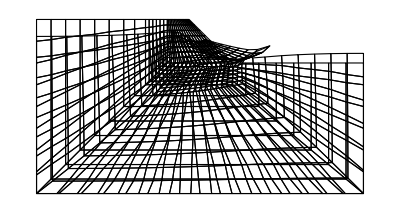

```mathematica
sol=solss[[18]];
scale=5;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]
```

```mathematica
soltalude
```

{{0.0582632,0.6542},{0.131375,1.47021},{0.16839,1.8753},{0.211331,2.33381},{0.255101,2.78415},{0.30038,3.22448},{0.342564,3.60002},{0.389501,3.96213},{0.423948,4.16505},{0.461101,4.24911},{0.486027,4.27668},{0.564268,4.33886},{0.625624,4.34516},{0.70239,4.35551},{0.778881,4.36015},{0.846662,4.36123},{0.923061,4.36577},{0.990432,4.36536}}

```mathematica
sol2
```

{{0,0},{0.0000809044,1.5}}

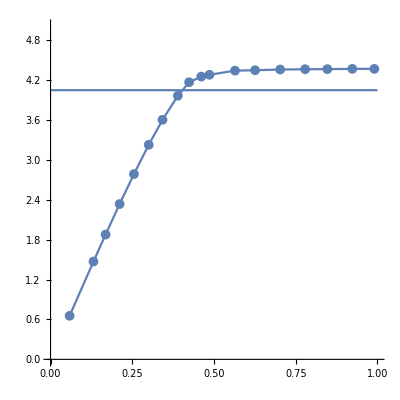

```mathematica
Show[ListLinePlot[soltalude,AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[4.045,{x,0,1}],PlotRange->{{0,1.},{0,5}}]
```

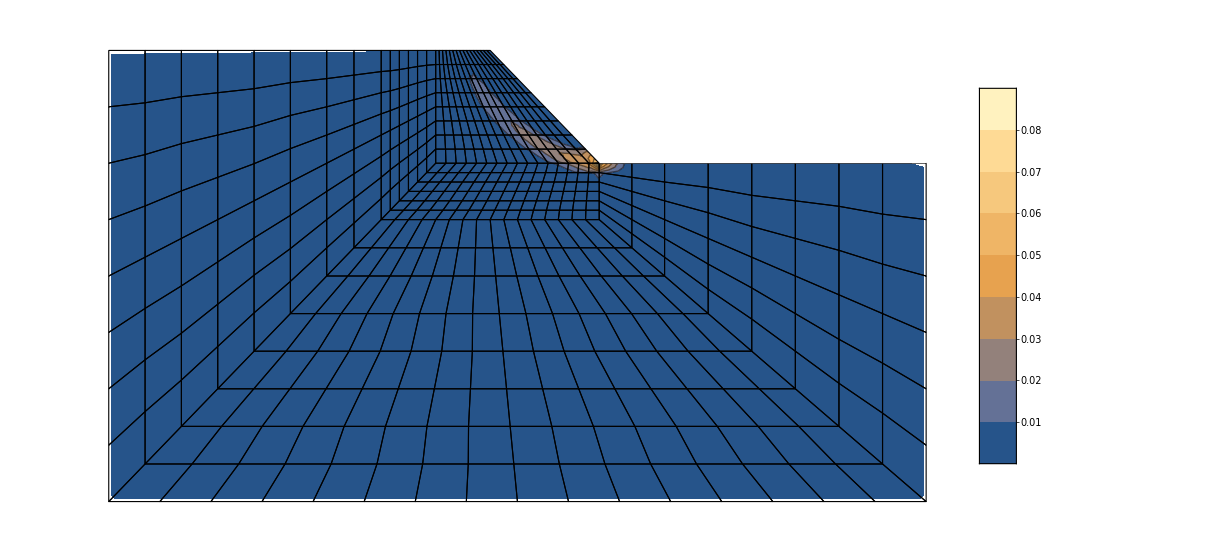

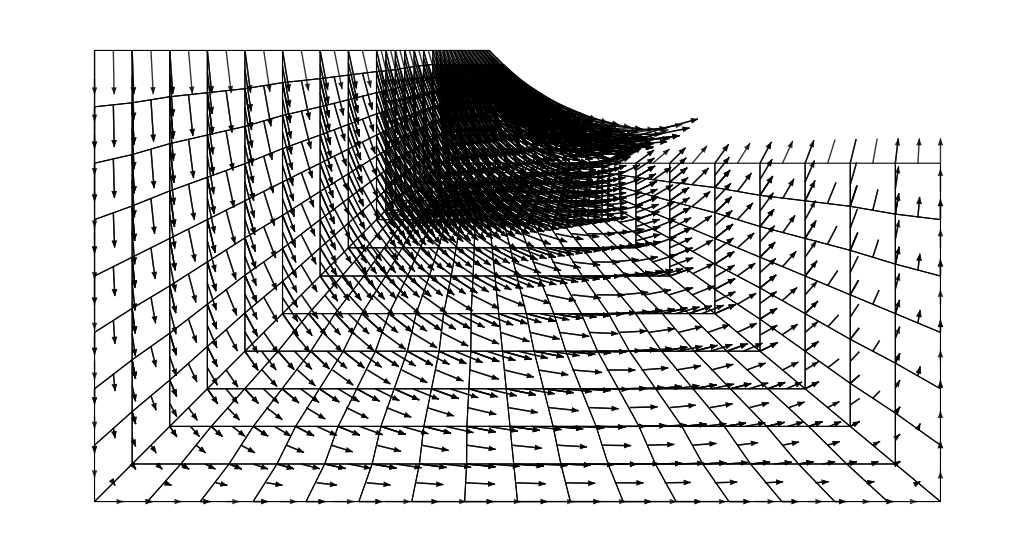

```mathematica
gph=Graphics[{White,Polygon[{{35,40},{45,30},{75,30},{75,40}}]}];
{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Opacity[0.8],Black,Arrowheads[.012],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
teste1=Table[{dgammasol[[9]][[i]][[1]],dgammasol[[9]][[i]][[2]],dgammasol[[9]][[i]][[3]]},{i,1,Length[dgammasol[[9]]]}];
Show[ListContourPlot[teste1,PlotLegends->{Placed[Automatic,{Left,Center}]}],gph,meshVis2,PlotRange->All,AspectRatio->Automatic,Frame->False]
sh=Show[meshVis1,arrows,PlotRange->All]
```